# 1 Dimensional FEM - Solver :

Example for a one dimensional diffusion problem with Neumann - Dirichlet boundary conditions

Name : Martin Obermaier
Lehrstuhl Theoretische Elektrotechnik und Prozessmodelle
BTU Cottbus
Datum :

This is a implemenation of the example 5.1 in the book "A first course in FEM", by Jacob Fish. It uses the implicit weak form to calculate the Matrix elements and forcing vector. It does not generate the weak form. This means the programm is only suited for diffusion like problems. This programm support a non equally spaced mesh and a non constant external force. It also allows to change the basis functions. *TODO* Implement a generator for the weak form , expand the the programm to multipble dimensions and boundry types.

## Setup for the Problem

```mathematica
ClearAll["Global`*"]
Needs["NDSolve`FEM`"];
LaunchKernels[4];
ParallelEvaluate[SystemID];
k=2.0;  (*thermal conductifity*)
L=4.0;      (*length of the object*)
A = 0.1; (*Area*) 
f[x_] := 5*Sin[x];  (*Force*)
Neu = 5; (*Neuman Boundry*)
Dir  = 0;   (*Dirichlet Boundry*)
NuNodes = 10;(*Number of Nodes in the problem*)
ExactSol[x_] :=21.3411 x+25 *Sin[x]
```

## Define the basis functions

```mathematica
Ne[x_,x1_,x2_]:= {{(x-x2)/(x1-x2),(x-x1)/(x2-x1)}}; (*Creation of linear Basisfunctions in 1D*)
Be[x_,x1_,x2_] := D[Ne[a,x1,x2],a]/.a->x;
```

## Calculate mesh

```mathematica
Parallelize[
Coor=Table[i*L/(NuNodes-1),{i,0,NuNodes-1},{j,1}];(*Calculate the Positions of each node*)
Lines =Table[i+j,{i,1,NuNodes-1},{j,0,1}] ;(*Create Elements for ploting*)
mesh= MeshRegion[Coor,Line[Lines]];
NuEl= MeshCellCount[mesh,1]; (*Number of Elements in the mesh*)
NuNoEl=Length[MeshCells[mesh,MeshCellIndex[mesh,1]][[1,1]]];(* Number of Nodes per Elements*)
]
```

## Calculate the elements

```mathematica
Ke[el_]:= k*A*NIntegrate[Transpose[Be[x,Coor[[el,1]],Coor[[el+1,1]]]].Be[x,Coor[[el,1]],Coor[[el+1,1]]],{x,Coor[[el,1]],Coor[[el+1,1]]}]
fe[el_] := NIntegrate[Transpose[Ne[x,Coor[[el,1]],Coor[[el+1,1]]]]*f[(Coor[[el+1,1]]+Coor[[el,1]])/2],{x,Coor[[el,1]],Coor[[el+1,1]]}] (*Definiton of the forcing element*)
```

## Build the system to be solved

```mathematica
SetSystemOptions["SparseArrayOptions"->{"TreatRepeatedEntries"->1}]; (*Make SpareArrays additive*)
pat1=Flatten[Table[Table[i,{i,1,NuNoEl}],NuNoEl]] (*Create Patterns shift matrices*)
pat2 =Flatten[Table[{i,i},{i,1,NuNoEl}]]
Parallelize[
connect=MeshCells[mesh,MeshCellIndex[mesh,1]][[All,1]]; (*Get Conection Matrix*)

Ig=connect [[All, pat1]]; (*First shift matrix*)
  Jg=connect [[All, pat2  ]];  (*second shift matrix*)
]
Kg=ConstantArray[0,{NuEl,NuNoEl^2}]; (*Create a Matrix with one row per Element and one column per entry in the Ke Matrix*)
For[i=1, i≤NuEl, i++,            (*Fill Matrix for each element*)
Kg[[i,All]]=Flatten[Ke[3]]; (*Flatten stiffness element*)
]
Parallelize[
K1=SparseArray[Transpose[{Flatten[Transpose[Ig]] ,Flatten[Transpose[Jg]]}]->Flatten[Transpose[Kg]]]; (*create stiffness Matrix*)
]


Parallelize[
Fe= ConstantArray[0,{ NuNodes,1}] ; (*Create Forcing-Vector (analog to the Stiffnes Matrix)*)
For[el=1 , el≤ NuEl,el++,
	mi = MeshCells[mesh,MeshCellIndex[mesh,1]][[el,1]];
	For[i = 1,i≤NuNoEl,i++,
                  fi=fe[el];
		ii= mi[[i]];
		Fe[[ii]]=(Fe[[ii]]+fi[[i]]);
		
	]
	]
]

NeuB= Table[KroneckerDelta[i,NuNodes]*(-A*Neu),{i,1,NuNodes},{j,1}]; (*Solve for the Neumann vector*)
F1=Fe+NeuB;
```

{1,2,1,2}

{1,1,2,2}

## Solve the system

```mathematica
Parallelize[
K=Take[K1,{2,NuNodes},{2,NuNodes}];
F=Take[F1,{2,NuNodes}]-Take[K1,{2,NuNodes},{1,1}]*Dir;
d = Prepend[LinearSolve[K,F],{Dir}]; (*Solve for Nodes and add Dirichlet Node*)
]
```

## Plot the solution

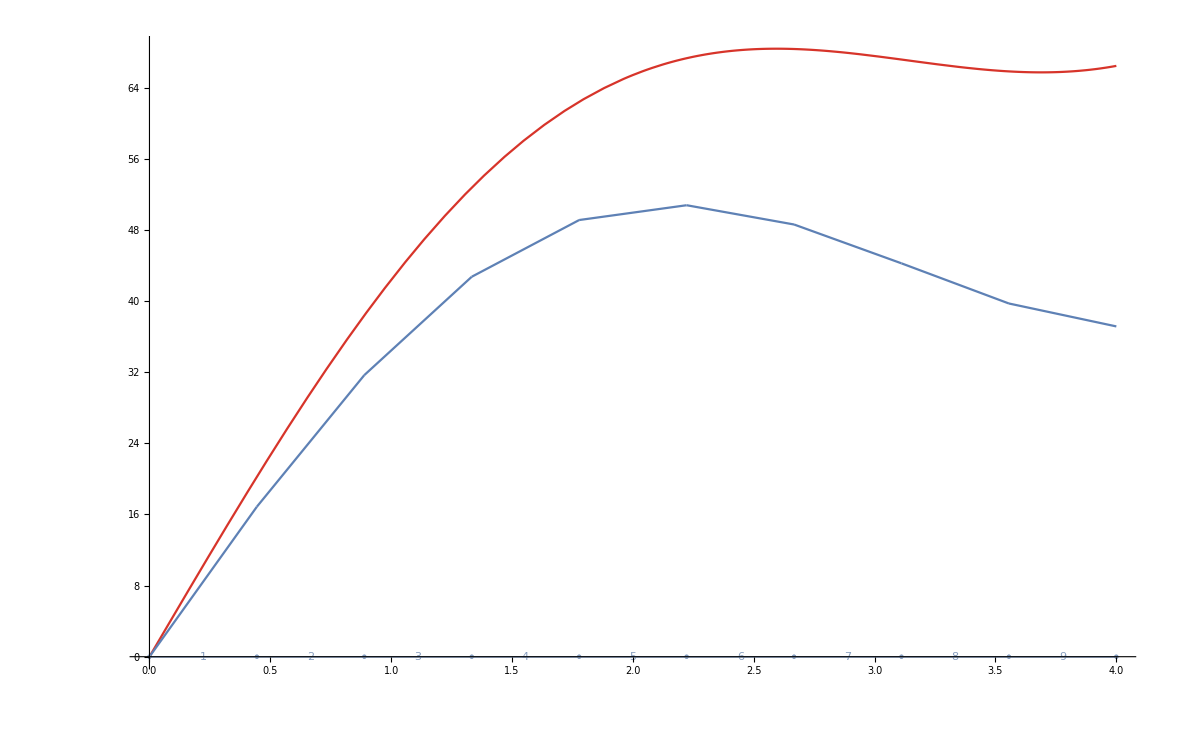

```mathematica
Parallelize[
function =Table[{(Ne[x,Coor[[i,1]],Coor[[i+1,1]]].{d[[MeshCells[mesh,MeshCellIndex[mesh,1]][[i,1]][[1]]]],d[[MeshCells[mesh,MeshCellIndex[mesh,1]][[i,1]][[2]]]]})[[1,1]],Coor[[i,1]],Coor[[i+1,1]]},{i,1,NuNodes-1}]; (*Combine the Basisfunctions*)
Show[Plot[ExactSol[x],{x,0,L},ColorFunction->"Rainbow"],Plot[#,{x,##2},PlotRange->All, AxesLabel->{"distance [m]","Temprature [°C]"},AxesOrigin->{0,0}]&@@@function,mesh ,HighlightMesh[mesh,Labeled[1,"Index"]]]
](*Plot the solutuion*)

CloseKernels[];
```